```mathematica
(*Compute the repo root from the notebook location*)repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
URoots[N[2,100]]
u0 = %[[4]]
```

{-0.25716617386463644393706302623770958083567636406323279490317435391000875677710996530673846256200111-0.14498540496176211586181447937960395873612907508198703648782573993296665019919773127762910090259482 ⅈ,-0.25716617386463644393706302623770958083567636406323279490317435391000875677710996530673846256200111+0.14498540496176211586181447937960395873612907508198703648782573993296665019919773127762910090259482 ⅈ,0.227203634857985759161254765346706290384224015255178461093477420691304642267091217742189796411130923,1.}

1.

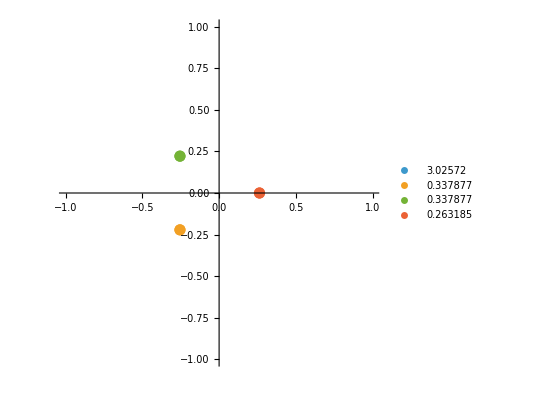

```mathematica
PlotURoots[N[1,100]]
```

```mathematica
b0 = NodalCurvebFrommu[N[2,100],u0]
```

-0.3819660112501051517954131656343618822796908201942371378645513772947395371810975502927927958106089

```mathematica
KerrDoranQ[b0]/(2Pi I)/.LiEval
```

0.0551589000381628983491141080294994227456724371824138676223158084267804417616716706244982779634919-0.584750831613469831108344339422151373612615844470651886935379744382584597390483314660777295412487 ⅈ

```mathematica
Pi/6//N
```

0.523599

```mathematica
u0 = URoots[N[1,100]][[4]]
```

0.263185269218743579065357060278145251896767028025740392847233274382509943322046211929710968647568384

```mathematica
b0 = NodalCurvebFrommu[1,u0]
```

-0.725149761049014866527565152463683894060127694261271422227462465469488441831473031269047768433093222+0.68859118789783872858051959055806444225530679847176447674205722337962953356247491861302058566205021 ⅈ

```mathematica
KerrDoranQ[b0]/(2Pi I)/.LiEval
```

0.184193533083328278281112707414501562738794690081586154019297422619339095109738026974056390832702-0.0833333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333333 ⅈ

```mathematica
KerrDoranQ[b0]/.LiEval
```

0.523598775598298873077107230546583814032861566562517636829157432051302734381034833104672470890353+1.15732210074666531243235075733319062483391568725435034244705938558241669693977914018093542083103 ⅈ

```mathematica
Pi/6//N
```

0.523599

```mathematica
(Pi/6+t I)/(2Pi I)//Simplify
```

-ⅈ/12+t/(2 π)